```mathematica
SetDirectory["D:/ML/Dropbox"]
```

D:\ML\Dropbox

```mathematica
FileNames["*","D:\\ML\\Code\\supacoo\\assign4"]
```

{D:\ML\Code\supacoo\assign4\input_corrected.txt,D:\ML\Code\supacoo\assign4\input.txt,D:\ML\Code\supacoo\assign4\main.cc,D:\ML\Code\supacoo\assign4\makefile,D:\ML\Code\supacoo\assign4\output_Earth.txt,D:\ML\Code\supacoo\assign4\output_Jupiter.txt,D:\ML\Code\supacoo\assign4\output_Mars.txt,D:\ML\Code\supacoo\assign4\output_Mercury.txt,D:\ML\Code\supacoo\assign4\output_Moon.txt,D:\ML\Code\supacoo\assign4\output_Neptune.txt,D:\ML\Code\supacoo\assign4\output_Saturn.txt,D:\ML\Code\supacoo\assign4\output_Sun.txt,D:\ML\Code\supacoo\assign4\output_Uranus.txt,D:\ML\Code\supacoo\assign4\output_Venus.txt,D:\ML\Code\supacoo\assign4\planetinfo.cc,D:\ML\Code\supacoo\assign4\planetinfo.h}

```mathematica
sundata=Import["output_Sun.txt","Table"];
sun=Table[{sundata[[n]][[3]],sundata[[n]][[4]]},{n,1,18001}];
```

```mathematica
mercurydata=Import["output_Mercury.txt","Table"];
mercury=Table[{mercurydata[[n]][[3]],mercurydata[[n]][[4]]},{n,1,18001}];
```

```mathematica
venusdata=Import["output_Venus.txt","Table"];
venus=Table[{venusdata[[n]][[3]],venusdata[[n]][[4]]},{n,1,18001}];
```

```mathematica
earthdata=Import["output_Earth.txt","Table"];
earth=Table[{earthdata[[n]][[3]],earthdata[[n]][[4]]},{n,1,18001}];
```

```mathematica
moondata=Import["output_Moon.txt","Table"];
moon=Table[{moondata[[n]][[3]],moondata[[n]][[4]]},{n,1,18001}];
```

```mathematica
marsdata=Import["output_Mars.txt","Table"];
mars=Table[{marsdata[[n]][[3]],marsdata[[n]][[4]]},{n,1,18001}];
```

```mathematica
jupiterdata=Import["output_Jupiter.txt","Table"];
jupiter=Table[{jupiterdata[[n]][[3]],jupiterdata[[n]][[4]]},{n,1,18001}];
```

```mathematica
saturndata=Import["output_Saturn.txt","Table"];
saturn=Table[{saturndata[[n]][[3]],saturndata[[n]][[4]]},{n,1,18001}];
```

```mathematica
uranusdata=Import["output_Uranus.txt","Table"];
uranus=Table[{uranusdata[[n]][[3]],uranusdata[[n]][[4]]},{n,1,18001}];
```

```mathematica
neptunedata=Import["output_Neptune.txt","Table"];
neptune=Table[{neptunedata[[n]][[3]],neptunedata[[n]][[4]]},{n,1,18001}];
```

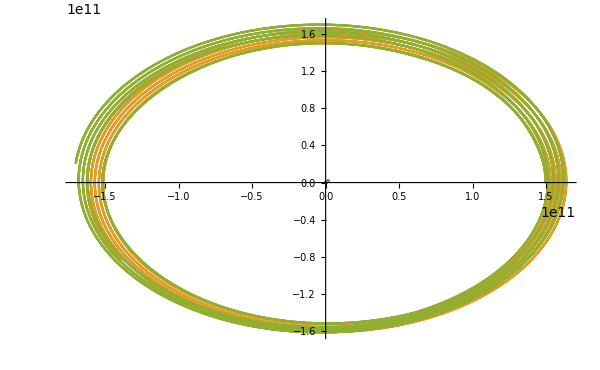

```mathematica
ListPlot[{sun, earth,moon},ImageSize->600]
```

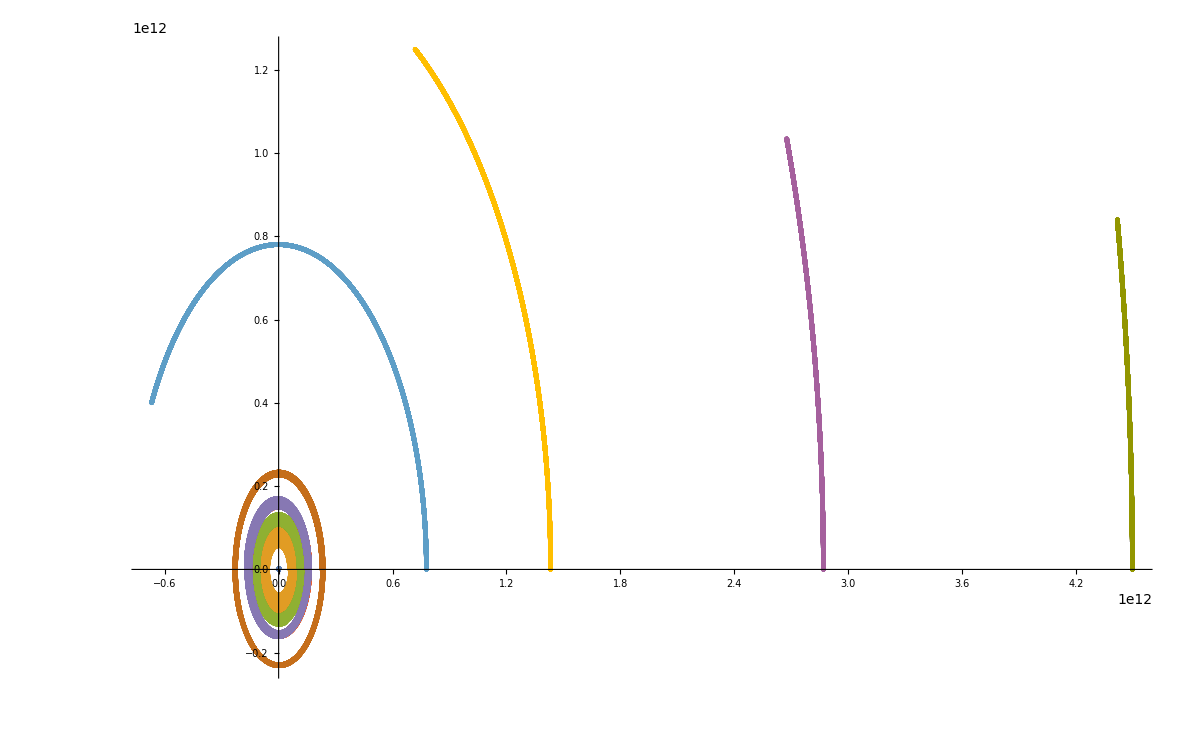

```mathematica
ListPlot[{sun, mercury,venus,earth,moon,mars,jupiter,saturn,uranus,neptune},ImageSize->1200]
```